{{300,123538},{400,52117.5},{500,26684.2},{600,15442.2},{700,9724.52},{800,6514.69},{900,4575.48},{1000,3335.52},{1100,2506.02},{1200,1930.28},{1300,1518.22},{1400,1215.57},{1500,988.295},{1600,814.335},{1700,678.917},{1800,571.933},{1900,486.299},{2000,416.94},{2100,360.168},{2200,313.253},{2300,274.145},{2400,241.285},{2500,213.473},{2600,189.776},{2700,169.461},{2800,151.946},{2900,136.764},{3000,123.538},{3100,111.963},{3200,101.792},{3300,92.8154},{3400,84.8647},{3500,77.7964},{9900,3.43761}}

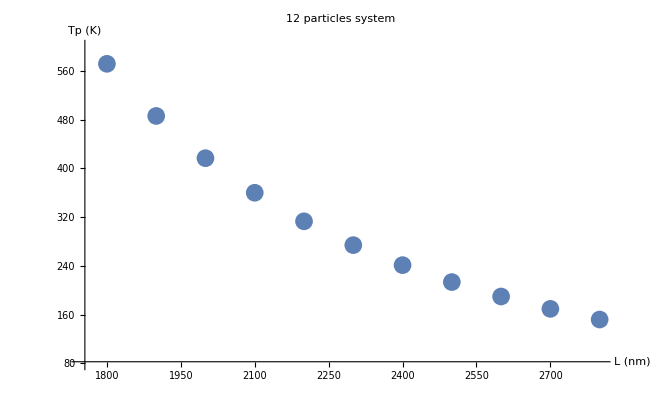

```mathematica
d={
123538,
52117.453640520194,
26684.243415261335,
15442.19079316868,
9724.516874904379,
6514.694919186868,
4575.480215635141,
3335.523209870203,
2506.0173820556456,
1930.2809569632695,
1518.2166534707558,
1215.5660672185872,
988.2947396095466,
814.3353169439542,
678.9169308313881,
571.9334608836026,
486.29861824167983,
416.9395177086751,
360.16792239620804,
313.2525728966183,
274.14525506097766,
241.28509349713377,
213.47263472863582,
189.77631844047497,
169.46130157351388,
151.94645851107822,
136.76415372066475,
123.53773799776083,
111.9634763179878,
101.79153766310333,
92.8154206486979,
84.86472585056062,
77.79643608066333
};
dd = Table[{(i+2)*100,d[[i]]},{i,1,Length[d]}];
dd = Append[dd,{9900,3.437614209303873}];
dd
ListPlot[dd,PlotRange->{{1750,2800},{80,600}},AxesLabel->{"L (nm)","Tp (K)"},PlotLabel->"12 particles system"]
```